```mathematica
(* mathematica*)
Clear[cr,cols,cr2,cr3,cr4,firstCols,s,s0]
allColors=ColorData["Legacy"][[3,1]];
firstCols={"White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+4]];
cr3[n_]:=cr3[n]=cols[[n+8]];
cr4[n_]:=cr4[n]=cols[[n+12]];
cr5[n_]:=cr5[n]=cols[[n+16]]
Clear[mu,a,b,A,B]
```

```mathematica
Factor[-1-3 x-x^2+x^3]
```

(1+x) (-1-2 x+x^2)

```mathematica
p[x_]=-1-3 x-x^2+x^3
```

```mathematica
NSolve[p[x]==0,x]
```

{{x→-1.},{x→-0.414214},{x→2.41421}}

```mathematica
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
```

```mathematica
s[1]=N[{{r[3],4},{0,1/r[1]}}]/Sqrt[Det[N[{{r[3],4},{0,1/r[1]}}]]]
s[2]=N[{{1,0},{4*I/(r[3]^2-1),1}}]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{0.-1.55377 ⅈ,0.-2.57438 ⅈ},{0.+0. ⅈ,0.+0.643594 ⅈ}}

{{1.,0.},{0.+0.828427 ⅈ,1.}}

{{0.+0.643594 ⅈ,0.+2.57438 ⅈ},{0.+0. ⅈ,0.-1.55377 ⅈ}}

{{1.+0. ⅈ,0.+0. ⅈ},{0.-0.828427 ⅈ,1.+0. ⅈ}}

```mathematica
qf=N[rotate[Pi/8]];qfi=Inverse[qf]
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
```

{{0.92388,0.382683},{-0.382683,0.92388}}

```mathematica
{a,b,A,B}=Table[N[qf.s[i].qfi],{i,4}]
```

{{{0.-0.321797 ⅈ,0.-2.97426 ⅈ},{0.-0.399878 ⅈ,0.-0.588383 ⅈ}},{{1.-0.292893 ⅈ,0.-0.12132 ⅈ},{0.+0.707107 ⅈ,1.+0.292893 ⅈ}},{{0.-0.588383 ⅈ,0.+2.97426 ⅈ},{0.+0.399878 ⅈ,0.-0.321797 ⅈ}},{{1.+0.292893 ⅈ,0.+0.12132 ⅈ},{0.-0.707107 ⅈ,1.-0.292893 ⅈ}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A]
Tr[A]
Det[B]
Tr[B]
```

1.+0. ⅈ

0.-0.91018 ⅈ

1.+5.55112×10^-17 ⅈ

2.+0. ⅈ

1.+0. ⅈ

0.-0.91018 ⅈ

1.-5.55112×10^-17 ⅈ

2.+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.000001 Round[(z1/z2)/0.000001];
Children[{z_,n_}]:={Affine[{a,b,A,B}[[#]].{z,1}],#}&/@Delete[Range[4],{3,4,1,2}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,A,B}[[i]].{0,1}],i},{i,1,4}],11];
ll=Length[aa1]
Last[aa1]
aa=aa1;
```

708588

{6.67195,0.876588}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->All];
```

```mathematica
dlst=Table[1+Mod[Floor[1+(1+Floor[12*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst]
Max[dlst]
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

6

78

```mathematica
g2=Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black];
```

```mathematica
(* end limit set*)
```

```mathematica
(*Perpendicular Hermetian inversion conformal map: z*Conjugate[z]/Abs[z]^2=1*)
```

```mathematica
bb=Delete[Reverse[Union[Table[{aa[[i,1]],-aa[[i,2]]}/(aa[[i,1]]^2+aa[[i,2]]^2),{i,Length[aa]}]]],1];
```

```mathematica
g1=ListPlot[bb,AspectRatio->Automatic,ColorFunction->"Rainbow",PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->All];
```

```mathematica
ptlst1a=Point[Developer`ToPackedArray[bb],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g5=Graphics[{PointSize[.001],ptlst1a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black];
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]]]];
```

```mathematica
ListPlot[bb1,PlotStyle->{{Yellow,PointSize[0.001]},{Orange,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->{-50,50}/10];
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];

g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->All],RasterSize->2000,ImageSize->2000];
```

```mathematica
cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False,ViewPoint->{2.1,2.1,2.1}],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_2group_Sqrt2_3realroots_cubic_QuasiconformalPi_8_limitset_11.jpg",GraphicsGrid[{{g0,g2},{g1,g5},{g3,g4}},ImageSize->5000]]
```

Nylander_2group_Sqrt2_3realroots_cubic_QuasiconformalPi_8_limitset_11.jpg

```mathematica
(*end*)
```

```mathematica
(*mathematica*)
```

```mathematica
(*Sqrt[2] Sierpinski three real root  cubic polynomial factor 8 group*)
```

```mathematica
p1=-1-3 x-x^2+x^3;
p2=1-3 x+x^2+x^3;
p3=-1+x+3 x^2+x^3;
p4=1+x-3 x^2+x^3;
```

```mathematica
f={x+1,p1,x-1,p2,x+1,p3,x-1,p4}
```

{1+x,-1-3 x-x^2+x^3,-1+x,1-3 x+x^2+x^3,1+x,-1+x+3 x^2+x^3,-1+x,1+x-3 x^2+x^3}

```mathematica
(* polynomial recursion in 8 factors*)
```

```mathematica
Clear[p,n,x]
```

```mathematica
p[1,x]=1
```

1

```mathematica
p[n_,x_]:=p[n,x]=p[n-1,x]*f[[1+Mod[n,8]]]
```

```mathematica
(*Polynomials*)
```

```mathematica
px=Table[Expand[FullSimplify[ExpandAll[p[i,x]]]],{i,11}]
```

{1,-1+x,-1+4 x-4 x^2+x^4,-1+3 x-4 x^3+x^4+x^5,1-4 x+12 x^3-2 x^4-12 x^5+4 x^7+x^8,-1+5 x-4 x^2-12 x^3+14 x^4+10 x^5-12 x^6-4 x^7+3 x^8+x^9,-1+4 x+4 x^2-32 x^3+19 x^4+56 x^5-56 x^6-32 x^7+45 x^8+4 x^9-12 x^10+x^12,-1+3 x+8 x^2-28 x^3-13 x^4+75 x^5-88 x^7+13 x^8+49 x^9-8 x^10-12 x^11+x^12+x^13,1-16 x^2+92 x^4-240 x^6+326 x^8-240 x^10+92 x^12-16 x^14+x^16,-1+x+16 x^2-16 x^3-92 x^4+92 x^5+240 x^6-240 x^7-326 x^8+326 x^9+240 x^10-240 x^11-92 x^12+92 x^13+16 x^14-16 x^15-x^16+x^17,-1+4 x+12 x^2-64 x^3-27 x^4+368 x^5-144 x^6-960 x^7+726 x^8+1304 x^9-1304 x^10-960 x^11+1194 x^12+368 x^13-592 x^14-64 x^15+155 x^16+4 x^17-20 x^18+x^20}

```mathematica
(* Coefficients triangle*)
```

```mathematica
v=Table[CoefficientList[p[i,x],x],{i,11}]
```

{{1},{-1,1},{-1,4,-4,0,1},{-1,3,0,-4,1,1},{1,-4,0,12,-2,-12,0,4,1},{-1,5,-4,-12,14,10,-12,-4,3,1},{-1,4,4,-32,19,56,-56,-32,45,4,-12,0,1},{-1,3,8,-28,-13,75,0,-88,13,49,-8,-12,1,1},{1,0,-16,0,92,0,-240,0,326,0,-240,0,92,0,-16,0,1},{-1,1,16,-16,-92,92,240,-240,-326,326,240,-240,-92,92,16,-16,-1,1},{-1,4,12,-64,-27,368,-144,-960,726,1304,-1304,-960,1194,368,-592,-64,155,4,-20,0,1}}

```mathematica
Flatten[Abs[v]]
```

{1,1,1,1,4,4,0,1,1,3,0,4,1,1,1,4,0,12,2,12,0,4,1,1,5,4,12,14,10,12,4,3,1,1,4,4,32,19,56,56,32,45,4,12,0,1,1,3,8,28,13,75,0,88,13,49,8,12,1,1,1,0,16,0,92,0,240,0,326,0,240,0,92,0,16,0,1,1,1,16,16,92,92,240,240,326,326,240,240,92,92,16,16,1,1,1,4,12,64,27,368,144,960,726,1304,1304,960,1194,368,592,64,155,4,20,0,1}

```mathematica
(*row sums*)
```

```mathematica
rsa0=Table[Apply[Plus,v[[i]]],{i,Length[v]}]
```

{1,0,0,0,0,0,0,0,0,0,0}

```mathematica
(*row (absolute value) sums*)
```

```mathematica
rsa=Table[Apply[Plus,Abs[v[[i]]]],{i,Length[v]}]
```

{1,2,10,10,36,66,266,300,1024,2048,8272}

```mathematica
TableForm[Table[CoefficientList[p[i,x],x],{i,11}]]
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 4 | -4 | 0 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 3 | 0 | -4 | 1 | 1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
1 | -4 | 0 | 12 | -2 | -12 | 0 | 4 | 1 |  |  |  |  |  |  |  |  |  |  |  | 
-1 | 5 | -4 | -12 | 14 | 10 | -12 | -4 | 3 | 1 |  |  |  |  |  |  |  |  |  |  | 
-1 | 4 | 4 | -32 | 19 | 56 | -56 | -32 | 45 | 4 | -12 | 0 | 1 |  |  |  |  |  |  |  | 
-1 | 3 | 8 | -28 | -13 | 75 | 0 | -88 | 13 | 49 | -8 | -12 | 1 | 1 |  |  |  |  |  |  | 
1 | 0 | -16 | 0 | 92 | 0 | -240 | 0 | 326 | 0 | -240 | 0 | 92 | 0 | -16 | 0 | 1 |  |  |  | 
-1 | 1 | 16 | -16 | -92 | 92 | 240 | -240 | -326 | 326 | 240 | -240 | -92 | 92 | 16 | -16 | -1 | 1 |  |  | 
-1 | 4 | 12 | -64 | -27 | 368 | -144 | -960 | 726 | 1304 | -1304 | -960 | 1194 | 368 | -592 | -64 | 155 | 4 | -20 | 0 | 1

```mathematica
(*Pictures*)
```

```mathematica
lvl=1024
```

1024

```mathematica
w=Table[CoefficientList[p[i,x],x],{i,lvl}];
```

```mathematica
ww=ParallelTable[Join[Mod[w[[i]],2],Table[0,{j,Length[w[[lvl]]]-Length[w[[i]]]}]],{i,Length[w]}];
```

```mathematica
Dimensions[ww]
```

{1024,2046}

```mathematica
g1=ListDensityPlot[ww,ColorFunction->"CMYKColors",ImageSize->2000];
```

```mathematica
Export["Sqrt2_three_real_root_cubic_triangle_recursive_Polynomial_1024_2046_g1.jpg",g1]
```

Sqrt2_three_real_root_cubic_triangle_recursive_Polynomial_1024_2046_g1.jpg

```mathematica
Clear[p,q]
```

```mathematica
p[x_]=px[[9]]
```

1-16 x^2+92 x^4-240 x^6+326 x^8-240 x^10+92 x^12-16 x^14+x^16

```mathematica
(*Polynomial expansion*)
```

```mathematica
q[x_]=ExpandAll[x^16*p[1/x]]
a=Abs[Table[-SeriesCoefficient[Series[1/p[x],{x,0,50}],m],{m,0,50,2}]]
```

1-16 x^2+92 x^4-240 x^6+326 x^8-240 x^10+92 x^12-16 x^14+x^16

{1,16,164,1392,10698,77488,539956,3662032,24345379,159389536,1030954744,6603137440,41949698516,264689227424,1660388880696,10363269171808,64398773626789,398641032334832,2459237831382332,15124916762215568,92767257168451166,567572462001477584,3464753534931793484,21107371032384574640,128345920348056026055,779080414903238523840}

```mathematica
Table[N[a[[i+1]]/a[[i]]],{i,Length[a]-1}]
```

{16.,10.25,8.4878,7.68534,7.24322,6.96825,6.78209,6.64805,6.54701,6.46815,6.40488,6.35299,6.30968,6.27297,6.24147,6.21414,6.1902,6.16905,6.15025,6.13341,6.11824,6.10451,6.09203,6.08062,6.07016}

```mathematica
x/.NSolve[p[x]==0,x]
```

{-2.41421,-2.41421,-1.00015,-1.00007,-0.999949,-0.999892,-0.414214,-0.414214,0.414214,0.414214,0.999878,0.999927,1.00006,1.00014,2.41421,2.41421}

```mathematica
r[x_]=p[x]/.x->x^(1/2)
```

1-16 x+92 x^2-240 x^3+326 x^4-240 x^5+92 x^6-16 x^7+x^8

```mathematica
x/.NSolve[r[x]==0,x]
```

{0.171573,0.171573,1.,1.,1.,1.,5.82843,5.82843}

```mathematica
qr[x_]=ExpandAll[x^8*r[1/x]]
ar=Abs[Table[-SeriesCoefficient[Series[1/qr[x],{x,0,50}],m],{m,0,50}]]
```

1-16 x+92 x^2-240 x^3+326 x^4-240 x^5+92 x^6-16 x^7+x^8

{1,16,164,1392,10698,77488,539956,3662032,24345379,159389536,1030954744,6603137440,41949698516,264689227424,1660388880696,10363269171808,64398773626789,398641032334832,2459237831382332,15124916762215568,92767257168451166,567572462001477584,3464753534931793484,21107371032384574640,128345920348056026055,779080414903238523840,4721643704466416401840,28573712360418220658240,172682706613785630893480,1042272053708228944011840,6283484697795445585692336,37839097099637656505927616,227631328617309907512077769,1368049797941325061003987152,8214392768335980679074337428,49280557744569497064379551408,295408733984745289792265571826,1769448276945393032148651980272,10590999732090893357771212324004,63348586511238159052048579959696,378663018904763932125268449407979,2262032487938262468786481250348320,13504787175280887219944385673883176,80580819202062601851897513386313184,480553644600431893558196011582985596,2864368019142236236496792777152193248,17064842778139893217752890660634759784,101618191526276861747003017021443307552,604846135331112801633829676467442173037,3598576091293369355596379365944925335728,21401113408475328252817307999172986407596}

```mathematica
Table[N[ar[[i+1]]/ar[[i]]],{i,Length[ar]-1}]
```

{16.,10.25,8.4878,7.68534,7.24322,6.96825,6.78209,6.64805,6.54701,6.46815,6.40488,6.35299,6.30968,6.27297,6.24147,6.21414,6.1902,6.16905,6.15025,6.13341,6.11824,6.10451,6.09203,6.08062,6.07016,6.06053,6.05165,6.04341,6.03576,6.02864,6.02199,6.01577,6.00994,6.00445,5.99929,5.99443,5.98983,5.98548,5.98136,5.97745,5.97373,5.9702,5.96683,5.96362,5.96056,5.95763,5.95483,5.95214,5.94957,5.94711}

```mathematica
(*end*)
```

```mathematica
(*Mathematica*)
```

```mathematica
(* three real root polynomials to middle levels {-5,5}*)
```

```mathematica
(* Delete[Reverse[Union[Flatten[Table[Table[Union[Table[If[Im[x/.NSolve[i+j*x+k*x^2+x^3==0,x][[1]]]==0&&Im[x/.NSolve[i+j*x+k*x^2+x^3==0,x][[2]]]==0,i+j*x+k*x^2+x^3,{}],{i,-1,1,2}]],{j,-5,5}],{k,-5,5}],2]]],1]*)
```

```mathematica
q={1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}
```

{1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}

```mathematica
(*solving for the basis matrix for 9 of the  cubic polynomial*)
```

```mathematica
Clear[m,p,x,a,b,x,q,w1,w2]
```

```mathematica
m={{a,0,1},{b,0,1},{0,c,0}}
```

{{a,0,1},{b,0,1},{0,c,0}}

```mathematica
p[x_]=CharacteristicPolynomial[m,x]
```

-a c+b c+c x+a x^2-x^3

```mathematica
w1=CoefficientList[p[x],x]
```

{-a c+b c,c,a,-1}

```mathematica
q={1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}
```

{1+5 x+5 x^2+x^3,-1+5 x+5 x^2+x^3,-1+4 x+5 x^2+x^3,-1+3 x+5 x^2+x^3,-1+2 x+5 x^2+x^3,-1+x+5 x^2+x^3,-1-x+5 x^2+x^3,-1-2 x+5 x^2+x^3,-1-3 x+5 x^2+x^3,-1-4 x+5 x^2+x^3,1-5 x+5 x^2+x^3,-1-5 x+5 x^2+x^3,-1+5 x^2+x^3,1+4 x+4 x^2+x^3,-1+3 x+4 x^2+x^3,-1+2 x+4 x^2+x^3,-1+x+4 x^2+x^3,-1-x+4 x^2+x^3,-1-2 x+4 x^2+x^3,-1-3 x+4 x^2+x^3,-1-4 x+4 x^2+x^3,1-5 x+4 x^2+x^3,-1-5 x+4 x^2+x^3,-1+4 x^2+x^3,1+3 x+3 x^2+x^3,-1+x+3 x^2+x^3,-1-x+3 x^2+x^3,-1-2 x+3 x^2+x^3,-1-3 x+3 x^2+x^3,1-4 x+3 x^2+x^3,-1-4 x+3 x^2+x^3,1-5 x+3 x^2+x^3,-1-5 x+3 x^2+x^3,-1+3 x^2+x^3,-1-x+2 x^2+x^3,-1-2 x+2 x^2+x^3,-1-3 x+2 x^2+x^3,1-4 x+2 x^2+x^3,-1-4 x+2 x^2+x^3,1-5 x+2 x^2+x^3,-1-5 x+2 x^2+x^3,-1+2 x^2+x^3,-1-x+x^2+x^3,-1-2 x+x^2+x^3,1-3 x+x^2+x^3,-1-3 x+x^2+x^3,1-4 x+x^2+x^3,-1-4 x+x^2+x^3,1-5 x+x^2+x^3,-1-5 x+x^2+x^3,1-x-x^2+x^3,1-2 x-x^2+x^3,1-3 x-x^2+x^3,-1-3 x-x^2+x^3,1-4 x-x^2+x^3,-1-4 x-x^2+x^3,1-5 x-x^2+x^3,-1-5 x-x^2+x^3,1-x-2 x^2+x^3,1-2 x-2 x^2+x^3,1-3 x-2 x^2+x^3,1-4 x-2 x^2+x^3,-1-4 x-2 x^2+x^3,1-5 x-2 x^2+x^3,-1-5 x-2 x^2+x^3,1-2 x^2+x^3,-1+3 x-3 x^2+x^3,1+x-3 x^2+x^3,1-x-3 x^2+x^3,1-2 x-3 x^2+x^3,1-3 x-3 x^2+x^3,1-4 x-3 x^2+x^3,-1-4 x-3 x^2+x^3,1-5 x-3 x^2+x^3,-1-5 x-3 x^2+x^3,1-3 x^2+x^3,-1+4 x-4 x^2+x^3,1+3 x-4 x^2+x^3,1+2 x-4 x^2+x^3,1+x-4 x^2+x^3,1-x-4 x^2+x^3,1-2 x-4 x^2+x^3,1-3 x-4 x^2+x^3,1-4 x-4 x^2+x^3,1-5 x-4 x^2+x^3,-1-5 x-4 x^2+x^3,1-4 x^2+x^3,1+5 x-5 x^2+x^3,-1+5 x-5 x^2+x^3,1+4 x-5 x^2+x^3,1+3 x-5 x^2+x^3,1+2 x-5 x^2+x^3,1+x-5 x^2+x^3,1-x-5 x^2+x^3,1-2 x-5 x^2+x^3,1-3 x-5 x^2+x^3,1-4 x-5 x^2+x^3,1-5 x-5 x^2+x^3,-1-5 x-5 x^2+x^3,1-5 x^2+x^3,1-2 x+x^3,-1-2 x+x^3,1-3 x+x^3,-1-3 x+x^3,1-4 x+x^3,-1-4 x+x^3,1-5 x+x^3,-1-5 x+x^3}

```mathematica
w2[j_]:=-CoefficientList[q[[j]],x]
```

```mathematica
Table[{q[[j]],m/.NSolve[Table[w1[[i]]-w2[j][[i]]==0,{i,3}],{a,b,c}]},{j,2,Length[q]}]
```

{{-1+5 x+5 x^2+x^3,{{{-5.,0,1},{-5.2,0,1},{0,-5.,0}}}},{-1+4 x+5 x^2+x^3,{{{-5.,0,1},{-5.25,0,1},{0,-4.,0}}}},{-1+3 x+5 x^2+x^3,{{{-5.,0,1},{-5.33333,0,1},{0,-3.,0}}}},{-1+2 x+5 x^2+x^3,{{{-5.,0,1},{-5.5,0,1},{0,-2.,0}}}},{-1+x+5 x^2+x^3,{{{-5.,0,1},{-6.,0,1},{0,-1.,0}}}},{-1-x+5 x^2+x^3,{{{-5.,0,1},{-4.,0,1},{0,1.,0}}}},{-1-2 x+5 x^2+x^3,{{{-5.,0,1},{-4.5,0,1},{0,2.,0}}}},{-1-3 x+5 x^2+x^3,{{{-5.,0,1},{-4.66667,0,1},{0,3.,0}}}},{-1-4 x+5 x^2+x^3,{{{-5.,0,1},{-4.75,0,1},{0,4.,0}}}},{1-5 x+5 x^2+x^3,{{{-5.,0,1},{-5.2,0,1},{0,5.,0}}}},{-1-5 x+5 x^2+x^3,{{{-5.,0,1},{-4.8,0,1},{0,5.,0}}}},{-1+5 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1+4 x+4 x^2+x^3,{{{-4.,0,1},{-3.75,0,1},{0,-4.,0}}}},{-1+3 x+4 x^2+x^3,{{{-4.,0,1},{-4.33333,0,1},{0,-3.,0}}}},{-1+2 x+4 x^2+x^3,{{{-4.,0,1},{-4.5,0,1},{0,-2.,0}}}},{-1+x+4 x^2+x^3,{{{-4.,0,1},{-5.,0,1},{0,-1.,0}}}},{-1-x+4 x^2+x^3,{{{-4.,0,1},{-3.,0,1},{0,1.,0}}}},{-1-2 x+4 x^2+x^3,{{{-4.,0,1},{-3.5,0,1},{0,2.,0}}}},{-1-3 x+4 x^2+x^3,{{{-4.,0,1},{-3.66667,0,1},{0,3.,0}}}},{-1-4 x+4 x^2+x^3,{{{-4.,0,1},{-3.75,0,1},{0,4.,0}}}},{1-5 x+4 x^2+x^3,{{{-4.,0,1},{-4.2,0,1},{0,5.,0}}}},{-1-5 x+4 x^2+x^3,{{{-4.,0,1},{-3.8,0,1},{0,5.,0}}}},{-1+4 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1+3 x+3 x^2+x^3,{{{-3.,0,1},{-2.66667,0,1},{0,-3.,0}}}},{-1+x+3 x^2+x^3,{{{-3.,0,1},{-4.,0,1},{0,-1.,0}}}},{-1-x+3 x^2+x^3,{{{-3.,0,1},{-2.,0,1},{0,1.,0}}}},{-1-2 x+3 x^2+x^3,{{{-3.,0,1},{-2.5,0,1},{0,2.,0}}}},{-1-3 x+3 x^2+x^3,{{{-3.,0,1},{-2.66667,0,1},{0,3.,0}}}},{1-4 x+3 x^2+x^3,{{{-3.,0,1},{-3.25,0,1},{0,4.,0}}}},{-1-4 x+3 x^2+x^3,{{{-3.,0,1},{-2.75,0,1},{0,4.,0}}}},{1-5 x+3 x^2+x^3,{{{-3.,0,1},{-3.2,0,1},{0,5.,0}}}},{-1-5 x+3 x^2+x^3,{{{-3.,0,1},{-2.8,0,1},{0,5.,0}}}},{-1+3 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1-x+2 x^2+x^3,{{{-2.,0,1},{-1.,0,1},{0,1.,0}}}},{-1-2 x+2 x^2+x^3,{{{-2.,0,1},{-1.5,0,1},{0,2.,0}}}},{-1-3 x+2 x^2+x^3,{{{-2.,0,1},{-1.66667,0,1},{0,3.,0}}}},{1-4 x+2 x^2+x^3,{{{-2.,0,1},{-2.25,0,1},{0,4.,0}}}},{-1-4 x+2 x^2+x^3,{{{-2.,0,1},{-1.75,0,1},{0,4.,0}}}},{1-5 x+2 x^2+x^3,{{{-2.,0,1},{-2.2,0,1},{0,5.,0}}}},{-1-5 x+2 x^2+x^3,{{{-2.,0,1},{-1.8,0,1},{0,5.,0}}}},{-1+2 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1-x+x^2+x^3,{{{-1.,0,1},{0.,0,1},{0,1.,0}}}},{-1-2 x+x^2+x^3,{{{-1.,0,1},{-0.5,0,1},{0,2.,0}}}},{1-3 x+x^2+x^3,{{{-1.,0,1},{-1.33333,0,1},{0,3.,0}}}},{-1-3 x+x^2+x^3,{{{-1.,0,1},{-0.666667,0,1},{0,3.,0}}}},{1-4 x+x^2+x^3,{{{-1.,0,1},{-1.25,0,1},{0,4.,0}}}},{-1-4 x+x^2+x^3,{{{-1.,0,1},{-0.75,0,1},{0,4.,0}}}},{1-5 x+x^2+x^3,{{{-1.,0,1},{-1.2,0,1},{0,5.,0}}}},{-1-5 x+x^2+x^3,{{{-1.,0,1},{-0.8,0,1},{0,5.,0}}}},{1-x-x^2+x^3,{{{1.,0,1},{0.,0,1},{0,1.,0}}}},{1-2 x-x^2+x^3,{{{1.,0,1},{0.5,0,1},{0,2.,0}}}},{1-3 x-x^2+x^3,{{{1.,0,1},{0.666667,0,1},{0,3.,0}}}},{-1-3 x-x^2+x^3,{{{1.,0,1},{1.33333,0,1},{0,3.,0}}}},{1-4 x-x^2+x^3,{{{1.,0,1},{0.75,0,1},{0,4.,0}}}},{-1-4 x-x^2+x^3,{{{1.,0,1},{1.25,0,1},{0,4.,0}}}},{1-5 x-x^2+x^3,{{{1.,0,1},{0.8,0,1},{0,5.,0}}}},{-1-5 x-x^2+x^3,{{{1.,0,1},{1.2,0,1},{0,5.,0}}}},{1-x-2 x^2+x^3,{{{2.,0,1},{1.,0,1},{0,1.,0}}}},{1-2 x-2 x^2+x^3,{{{2.,0,1},{1.5,0,1},{0,2.,0}}}},{1-3 x-2 x^2+x^3,{{{2.,0,1},{1.66667,0,1},{0,3.,0}}}},{1-4 x-2 x^2+x^3,{{{2.,0,1},{1.75,0,1},{0,4.,0}}}},{-1-4 x-2 x^2+x^3,{{{2.,0,1},{2.25,0,1},{0,4.,0}}}},{1-5 x-2 x^2+x^3,{{{2.,0,1},{1.8,0,1},{0,5.,0}}}},{-1-5 x-2 x^2+x^3,{{{2.,0,1},{2.2,0,1},{0,5.,0}}}},{1-2 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1+3 x-3 x^2+x^3,{{{3.,0,1},{2.66667,0,1},{0,-3.,0}}}},{1+x-3 x^2+x^3,{{{3.,0,1},{4.,0,1},{0,-1.,0}}}},{1-x-3 x^2+x^3,{{{3.,0,1},{2.,0,1},{0,1.,0}}}},{1-2 x-3 x^2+x^3,{{{3.,0,1},{2.5,0,1},{0,2.,0}}}},{1-3 x-3 x^2+x^3,{{{3.,0,1},{2.66667,0,1},{0,3.,0}}}},{1-4 x-3 x^2+x^3,{{{3.,0,1},{2.75,0,1},{0,4.,0}}}},{-1-4 x-3 x^2+x^3,{{{3.,0,1},{3.25,0,1},{0,4.,0}}}},{1-5 x-3 x^2+x^3,{{{3.,0,1},{2.8,0,1},{0,5.,0}}}},{-1-5 x-3 x^2+x^3,{{{3.,0,1},{3.2,0,1},{0,5.,0}}}},{1-3 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{-1+4 x-4 x^2+x^3,{{{4.,0,1},{3.75,0,1},{0,-4.,0}}}},{1+3 x-4 x^2+x^3,{{{4.,0,1},{4.33333,0,1},{0,-3.,0}}}},{1+2 x-4 x^2+x^3,{{{4.,0,1},{4.5,0,1},{0,-2.,0}}}},{1+x-4 x^2+x^3,{{{4.,0,1},{5.,0,1},{0,-1.,0}}}},{1-x-4 x^2+x^3,{{{4.,0,1},{3.,0,1},{0,1.,0}}}},{1-2 x-4 x^2+x^3,{{{4.,0,1},{3.5,0,1},{0,2.,0}}}},{1-3 x-4 x^2+x^3,{{{4.,0,1},{3.66667,0,1},{0,3.,0}}}},{1-4 x-4 x^2+x^3,{{{4.,0,1},{3.75,0,1},{0,4.,0}}}},{1-5 x-4 x^2+x^3,{{{4.,0,1},{3.8,0,1},{0,5.,0}}}},{-1-5 x-4 x^2+x^3,{{{4.,0,1},{4.2,0,1},{0,5.,0}}}},{1-4 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1+5 x-5 x^2+x^3,{{{5.,0,1},{5.2,0,1},{0,-5.,0}}}},{-1+5 x-5 x^2+x^3,{{{5.,0,1},{4.8,0,1},{0,-5.,0}}}},{1+4 x-5 x^2+x^3,{{{5.,0,1},{5.25,0,1},{0,-4.,0}}}},{1+3 x-5 x^2+x^3,{{{5.,0,1},{5.33333,0,1},{0,-3.,0}}}},{1+2 x-5 x^2+x^3,{{{5.,0,1},{5.5,0,1},{0,-2.,0}}}},{1+x-5 x^2+x^3,{{{5.,0,1},{6.,0,1},{0,-1.,0}}}},{1-x-5 x^2+x^3,{{{5.,0,1},{4.,0,1},{0,1.,0}}}},{1-2 x-5 x^2+x^3,{{{5.,0,1},{4.5,0,1},{0,2.,0}}}},{1-3 x-5 x^2+x^3,{{{5.,0,1},{4.66667,0,1},{0,3.,0}}}},{1-4 x-5 x^2+x^3,{{{5.,0,1},{4.75,0,1},{0,4.,0}}}},{1-5 x-5 x^2+x^3,{{{5.,0,1},{4.8,0,1},{0,5.,0}}}},{-1-5 x-5 x^2+x^3,{{{5.,0,1},{5.2,0,1},{0,5.,0}}}},{1-5 x^2+x^3,{{a,0,1},{b,0,1},{0,c,0}}},{1-2 x+x^3,{{{0.,0,1},{-0.5,0,1},{0,2.,0}}}},{-1-2 x+x^3,{{{0.,0,1},{0.5,0,1},{0,2.,0}}}},{1-3 x+x^3,{{{0.,0,1},{-0.333333,0,1},{0,3.,0}}}},{-1-3 x+x^3,{{{0.,0,1},{0.333333,0,1},{0,3.,0}}}},{1-4 x+x^3,{{{0.,0,1},{-0.25,0,1},{0,4.,0}}}},{-1-4 x+x^3,{{{0.,0,1},{0.25,0,1},{0,4.,0}}}},{1-5 x+x^3,{{{0.,0,1},{-0.2,0,1},{0,5.,0}}}},{-1-5 x+x^3,{{{0.,0,1},{0.2,0,1},{0,5.,0}}}}}

```mathematica
(* two generator 3x3 extended Sqrt[2] root cubic  Polynomial group*)
Clear[p]
s[1]={{1,0,1},{4/3,0,1},{0,3,0}}
s[2]=-s[1]
s[3]=Inverse[s[1]]
s[4]=Inverse[s[2]]
```

{{1,0,1},{4/3,0,1},{0,3,0}}

{{-1,0,-1},{-4/3,0,-1},{0,-3,0}}

{{-3,3,0},{0,0,1/3},{4,-3,0}}

{{3,-3,0},{0,0,-1/3},{-4,3,0}}

```mathematica
p[1]=-CharacteristicPolynomial[s[1],x]
```

-1-3 x-x^2+x^3

```mathematica
p[2]=-CharacteristicPolynomial[s[2],x]
```

1-3 x+x^2+x^3

```mathematica
p[3]=-CharacteristicPolynomial[s[3],x]
```

-1+x+3 x^2+x^3

```mathematica
p[4]=-CharacteristicPolynomial[s[4],x]
```

1+x-3 x^2+x^3

```mathematica
Table[Det[s[i]],{i,4}]
```

{1,-1,1,-1}

```mathematica
Table[x/.NSolve[p[i]==0,x],{i,4}]
```

{{-1.,-0.414214,2.41421},{-2.41421,0.414214,1.},{-2.41421,-1.,0.414214},{-0.414214,1.,2.41421}}

```mathematica
Table[Tr[s[i]],{i,4}]
```

{1,-1,-3,3}

```mathematica
(* Casimir invariant*)
```

```mathematica
Sum[s[i].s[i],{i,4}]
```

{{20,-12,4},{16/3,4,8/3},{-16,24,4}}

```mathematica
(*Killing vectors*)
```

```mathematica
kl=Table[s[i].{1,1,1},{i,4}]
```

{{2,7/3,3},{-2,-7/3,-3},{0,1/3,1},{0,-1/3,-1}}

```mathematica
(*Pseudo-Cartan matrix*)
```

```mathematica
kt=kl.Transpose[kl]
```

{{166/9,-166/9,34/9,-34/9},{-166/9,166/9,-34/9,34/9},{34/9,-34/9,10/9,-10/9},{-34/9,34/9,-10/9,10/9}}

```mathematica
eg0=N[Eigenvalues[kt]]//Chop
```

{38.464,0.647069,0,0}

```mathematica
Apply[Plus,eg0]
```

39.1111

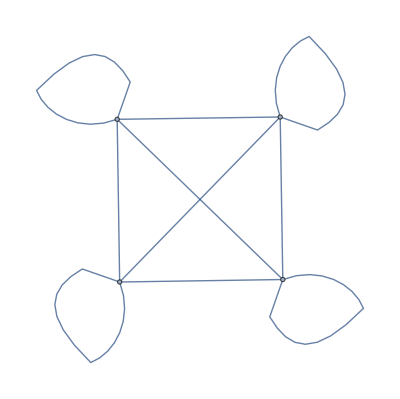

```mathematica
WeightedAdjacencyGraph[kt]
```

```mathematica
Transpose[kl].kl
```

{{8,28/3,12},{28/3,100/9,44/3},{12,44/3,20}}

```mathematica
(* Cartan matrix*)
```

```mathematica
ct=Table[2*kl[[i]].kl[[j]]/(kl[[i]].kl[[i]]),{i,4},{j,4}]
```

{{2,-2,34/83,-34/83},{-2,2,-34/83,34/83},{34/5,-34/5,2,-2},{-34/5,34/5,-2,2}}

```mathematica
MatrixForm[ct]
```

(2 | -2 | 34/83 | -34/83
-2 | 2 | -34/83 | 34/83
34/5 | -34/5 | 2 | -2
-34/5 | 34/5 | -2 | 2)

```mathematica
eg=N[Eigenvalues[ct]]//Chop
```

{7.33799,0.662011,0,0}

```mathematica
Apply[Plus,eg]
```

8.

```mathematica
WeightedAdjacencyGraph[ct]
```

-Graphics-

```mathematica
(*end*)
```